# Words

Peter Cullen Burbery

Abstract

## Investigation

I was reading an Elementary Introduction to the Wolfram language and working on some exercises for words and I noticed that adjectives seemed longer than nouns, so I decided to investigate the matter with statistics. My hypothesis that I will be exploring with statistics in Mathematica is that adjectives are longer than nouns overall.

I used as many statistical tools as I could to compare the lengths of adjectives and nouns. I am taking STA 345—Applied Probability and Statistics and STA 445—Probability and Statistics I right now so I thought this

I left other parts out like verbs because there's not as much data. I need lots of data and there are two few verbs to make good analysis. I also think its more complicated to compare 3 at once, though I guess it could be done.

A quick look shows that the 19 largest verbs aren't that interesting, in my opinion:

```mathematica
TakeLargestBy[WordList["Verb"],StringLength,19]
```

{institutionalize,intercommunicate,compartmentalize,internationalize,conventionalize,professionalize,hyperventilate,discountenance,contraindicate,overgeneralize,counterbalance,circumnavigate,sentimentalize,overcompensate,interpenetrate,disenfranchise,misappropriate,depersonalize,dematerialize}

The longest words are also smaller than nouns and adjectives, which have lengths of over 20.

```mathematica
ReverseSort[StringLength[WordList["Verb"]]][[4;;19]]
```

{16,15,15,14,14,14,14,14,14,14,14,14,14,14,13,13}

This is how the mass of the wordlist is divided, for example.

```mathematica
PieChart[AssociationMap[Length[WordList[#]]&,{"Noun","Verb","Adjective"}],ChartLabels->Automatic,PlotTheme->"Web"]
```

-Graphics-

I noticed that adjectives tend to be longer.

I will Mathematica to investigate if this holds true for all the words in WordList.

```mathematica
TakeLargestBy[WordList["Adjective"],StringLength,12]
```

{electroencephalographic,counterrevolutionary,nonrepresentational,interdenominational,noninterchangeable,indistinguishable,interdepartmental,deconstructionist,electromechanical,interdisciplinary,institutionalized,counterproductive}

I would like to mention that there is a relationship

```mathematica
WordData["electroencephalographicness"]
```

{}

```mathematica
adjectivesData=StringLength[WordList["Adjective"]];
```

```mathematica
nounData=StringLength[WordList["Noun"]];
```

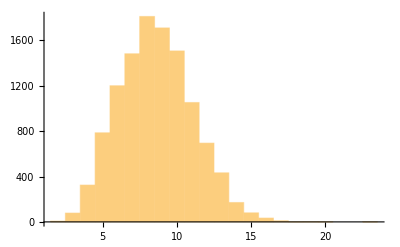

```mathematica
Histogram[adjectivesData]
```

I will also analyze other statistics for nouns and adjectives. I will first find the exact answer and then compute the numerical answer on the next line unless the answer is an exact integer for both nouns and adjectives.

I would like to mention that I am taking two courses right now and think analyzing word lengths is interesting. I am taking Probability and Statistics and Applied Probability and Statistics, so I think its interesting to analyze word lengths from this perspective.

I would also like to mention that I don't fully understand what some of the more advanced statistical functions like Qn dispersion do, but I think they're worth including anyway. There are some statistical functions that I wanted to use because they were in the guides Descriptive Statistics and Statistical Visualization but that I couldn't use because the data type wasn't right for example Covariance, Correlation, SpatialMedian, and Histogram3D.

### Location statistics for lengths of adjectives and nouns

#### Mean

```mathematica
{Mean[adjectivesData],Mean[nounData]}
```

{97999/11392,196846/24493}

```mathematica
N[{Mean[adjectivesData],Mean[nounData]}]
```

{8.60244,8.03683}

I think its interesting adjectives are longer than nouns on average.

#### Median

```mathematica
{Median[adjectivesData],Median[nounData]}
```

{9,8}

The median is also higher for adjectives.

#### Mode

```mathematica
{Commonest[adjectivesData],Commonest[nounData]}
```

{{8},{8}}

The mode is the same, however.

#### Trimmed mean

Compute the 5% trimmed mean.

```mathematica
{TrimmedMean[adjectivesData],TrimmedMean[nounData]}
```

{43876/5127,175209/22045}

```mathematica
N[{TrimmedMean[adjectivesData],TrimmedMean[nounData]}]
```

{8.55783,7.94779}

The 5% trimmed mean for adjectives is also greater.

#### Winsorized mean

Compute the 5% winsorized mean.

```mathematica
{WinsorizedMean[adjectivesData],WinsorizedMean[nounData]}
```

{48997/5696,196017/24493}

```mathematica
N[{WinsorizedMean[adjectivesData],WinsorizedMean[nounData]}]
```

{8.602,8.00298}

The 5 % winsorized mean is also higher for adjectives than nouns.

#### Biweight location

Compute the biweight location which weights data points further from the mean less.

```mathematica
{BiweightLocation[adjectivesData],BiweightLocation[nounData]}
```

{8.50764,7.9005}

The biweight location is also higher for adjectives than nouns. The biweight location is a robust location estimator.

### Dispersion statistics for lengths of adjectives and nouns

#### Variance

```mathematica
{Variance[adjectivesData],Variance[nounData]}
```

{792501023/129766272,711475857/99980426}

```mathematica
N[{Variance[adjectivesData],Variance[nounData]}]
```

{6.10714,7.11615}

Based on the variance, we can conclude that nouns have a greater spread in their lengths than adjectives.

#### Variance with uncertainty

The resource function variance around adds uncertainty to the variance calculated.

```mathematica
{ResourceFunction["VarianceAround"][adjectivesData],ResourceFunction["VarianceAround"][nounData]}
```

{6.110.08,7.120.06}

#### Trimmed variance

Compute the 5% trimmed variance.

```mathematica
{TrimmedVariance[adjectivesData],TrimmedVariance[nounData]}
```

{211125790/52567131,557567126/121489995}

```mathematica
N[{TrimmedVariance[adjectivesData],TrimmedVariance[nounData]}]
```

{4.01631,4.58941}

The 5% trimmed variance also supports the conclusion that the lengths of nouns are more spread out than the lengths of adjectives.

#### Winsorized variance

Compute the 5% winsorized variance.

```mathematica
{WinsorizedVariance[adjectivesData],WinsorizedVariance[nounData]}
```

{169705127/32441568,927138320/149970639}

```mathematica
N[{WinsorizedVariance[adjectivesData],WinsorizedVariance[nounData]}]
```

{5.2311,6.18213}

The 5% winsorized mean adds further support to the conclusion that the lengths of nouns demonstrate more spread than the lengths of adjectives.

#### Standard deviation

```mathematica
{StandardDeviation[adjectivesData],StandardDeviation[nounData]}
```

{(√(792501023/2027598))/8,3 √(79052873/99980426)}

```mathematica
N[{StandardDeviation[adjectivesData],StandardDeviation[nounData]}]
```

{2.47126,2.66761}

```mathematica
Subtract@@N[{StandardDeviation[adjectivesData],StandardDeviation[nounData]}]
```

-0.196348

The standard deviation is higher for nouns.

#### Mean deviation

```mathematica
{MeanDeviation[adjectivesData],MeanDeviation[nounData]}
```

{32478849/16222208,1266082056/599907049}

```mathematica
N[{MeanDeviation[adjectivesData],MeanDeviation[nounData]}]
```

{2.00212,2.11046}

```mathematica
Subtract@@N[{MeanDeviation[adjectivesData],MeanDeviation[nounData]}]
```

-0.108341

The mean deviation of adjectives and nouns is closer than the standard deviation of adjectives and nouns.

#### Median deviation

```mathematica
{MedianDeviation[adjectivesData],MedianDeviation[nounData]}
```

{2,2}

The median deviation is the same.

#### Quartile deviation

```mathematica
{QuartileDeviation[adjectivesData],QuartileDeviation[nounData]}
```

{3/2,2}

```mathematica
N[{QuartileDeviation[adjectivesData],QuartileDeviation[nounData]}]
```

{1.5,2.}

The quartile deviation is bigger for nouns than adjectives.

#### Interquartile range

```mathematica
{InterquartileRange[adjectivesData],InterquartileRange[nounData]}
```

{3,4}

The interquartile range is also higher than for nouns than adjectives.

#### Qn dispersion

The Qn dispersion is a robust statistic that measures dispersion.

```mathematica
{QnDispersion[adjectivesData],QnDispersion[nounData]}
```

{2.2184,2.21902}

```mathematica
Subtract@@{QnDispersion[adjectivesData],QnDispersion[nounData]}
```

-0.00061315

The lengths of nouns and adjectives are virtually indistinguishable with regard to the robust dispersion measure Qn dispersion.

#### Sn dispersion

The Sn dispersion is also a robust statistic that measures dispersion.

```mathematica
{SnDispersion[adjectivesData],SnDispersion[nounData]}
```

{2.3852,2.38528}

```mathematica
Subtract@@{SnDispersion[adjectivesData],SnDispersion[nounData]}
```

-0.0000876477

The lengths of nouns and adjectives are also virtually indistinguishable with regard to the robust dispersion measure Sn dispersion.

#### Biweight mid-variance

Biweight mid-variance is a robust dispersion estimator.

```mathematica
{BiweightMidvariance[adjectivesData],BiweightMidvariance[nounData]}
```

{809752516374624640/125638526379294009,18120274105518140801/2535655457678918450}

```mathematica
N[{BiweightMidvariance[adjectivesData],BiweightMidvariance[nounData]}]
```

{6.4451,7.14619}

The biweight mid-variance is noticeably bigger for nouns than adjectives.

### Shape statistics for lengths of adjectives and nouns

#### Skewness

```mathematica
{Skewness[adjectivesData],Skewness[nounData]}
```

{5976946253406/(792501023 √792501023),21462800200487/(2134427571 √474317238)}

```mathematica
N[{Skewness[adjectivesData],Skewness[nounData]}]
```

{0.267904,0.461711}

Positive skewness indicates a long right tail, so we can conclude that both distributions have long right tails but nouns have a longer right tail.

#### Kurtosis

```mathematica
{Kurtosis[adjectivesData],Kurtosis[nounData]}
```

{1848486170139694781/628057871456046529,561717051081936751/178658080621370982}

```mathematica
N[{Kurtosis[adjectivesData],Kurtosis[nounData]}]
```

{2.94318,3.14409}

A distribution with positive excess kurtosis is named leptokurtic or leptokurtotic. Leptokurtic distributions have fatter tails.

We can conclude both adjectives and nouns have a leptokurtic distribution and fat tails, but nouns have a fatter tail.

#### Quartile skewness

```mathematica
{QuartileSkewness[adjectivesData],QuartileSkewness[nounData]}
```

{-1/3,0}

```mathematica
N[{QuartileSkewness[adjectivesData],QuartileSkewness[nounData]}]
```

{-0.333333,0.}

Positive quartile skewness indicates the median is closer to q1 than q3 and negative quartile skewness indicates the median is closer to the upper quartile. Therefore, the adjectives median is closer to the upper quartile, and the noun's median is not skewed either way.

#### Entropy

```mathematica
{Entropy[adjectivesData],Entropy[nounData]}
```

{1/11392(-2 Log[2]-7 Log[7]-10 Log[10]-34 Log[34]-78 Log[78]-80 Log[80]-171 Log[171]-325 Log[325]-433 Log[433]-695 Log[695]-786 Log[786]-1053 Log[1053]-1201 Log[1201]-1483 Log[1483]-1508 Log[1508]-1711 Log[1711]-1812 Log[1812])+Log[11392],1/24493(-2 Log[2]-5 Log[5]-6 Log[6]-14 Log[14]-34 Log[34]-47 Log[47]-95 Log[95]-199 Log[199]-380 Log[380]-498 Log[498]-719 Log[719]-1075 Log[1075]-1576 Log[1576]-1671 Log[1671]-2233 Log[2233]-2436 Log[2436]-3014 Log[3014]-3296 Log[3296]-3571 Log[3571]-3621 Log[3621])+Log[24493]}

```mathematica
N[{Entropy[adjectivesData],Entropy[nounData]}]
```

{2.31243,2.37429}

Entropy calculates the base ⅇ information entropy of the values in a list.

Nouns have more entropy than adjectives.

#### Tsallis entropy

I can compute a generalization of entropy with a resource function.

```mathematica
ResourceFunction["TsallisEntropy"][adjectivesData,2,1]
```

9602891404/9603804001

```mathematica
N[ResourceFunction["TsallisEntropy"][adjectivesData,2,1]]
```

0.999905

#### Estimated distribution

Estimate a normal distribution to fit adjectives and nouns.

```mathematica
{EstimatedDistribution[adjectivesData,NormalDistribution[b,c]],EstimatedDistribution[nounData,NormalDistribution[b,c]]}
```

{NormalDistribution[8.60244,2.47115],NormalDistribution[8.03683,2.66756]}

### General statistics for lengths of adjectives and nouns

I copied this function that creates a grid from the documentation:

```mathematica
FormulaGrid[list_,type_]:=Grid[Transpose[{list}],Alignment->{Left,Automatic},Background->{None,{{Lighter[Blend[Switch[type,M,{Blue,Green},CM,{Red,Orange},FM,{Magenta,Cyan},C,{Purple,Red}]],.8],White}}},Dividers->{None,{Darker[Gray,.6],{False},Darker[Gray,.6]}},ItemSize->30]
```

I will use this function to make tables of different moments and statistics for adjectives and nouns.

#### Moment

```mathematica
{FormulaGrid[Table[Moment[adjectivesData,k]//Together,{k,5}],M],FormulaGrid[Table[Moment[nounData,k]//Together,{k,5}],M]}
```

{97999/11392
912597/11392
9093499/11392
96109317/11392
1070621419/11392,196846/24493
1756306/24493
17131246/24493
180528034/24493
2036572726/24493}

```mathematica
{FormulaGrid[Table[N@Moment[adjectivesData,k]//Together,{k,5}],M],FormulaGrid[Table[N@Moment[nounData,k]//Together,{k,5}],M]}
```

{8.60244
80.1086
798.236
8436.56
93980.1,8.03683
71.7064
699.434
7370.6
83149.2}

#### Central Moment

```mathematica
{FormulaGrid[Table[CentralMoment[adjectivesData,k]//Simplify,{k,5}],CM],FormulaGrid[Table[CentralMoment[nounData,k]//Simplify,{k,5}],CM]}
```

{0
792501023/129777664
2988473126703/739213574144
1848486170139694781/16842242073296896
13606808658404437431375/47966705424749559808,0
4268855142/599907049
128776801202922/14693523351157
57295139210357548602/359888467439888401
5492092518183034220371050/8814748233005186605693}

```mathematica
{FormulaGrid[Table[N@CentralMoment[adjectivesData,k]//Simplify,{k,5}],CM],FormulaGrid[Table[N@CentralMoment[nounData,k]//Simplify,{k,5}],CM]}
```

{0.
6.10661
4.04277
109.753
283.672,0.
7.11586
8.76419
159.202
623.057}

#### Factorial moment

```mathematica
{FormulaGrid[Table[FactorialMoment[adjectivesData,k]//Simplify,{k,5}],FM],FormulaGrid[Table[FactorialMoment[nounData,k]//Simplify,{k,5}],FM]}
```

{97999/11392
407299/5696
3275853/5696
3187431/712
48065355/1424,196846/24493
222780/3499
1750860/3499
95878848/24493
747795000/24493}

```mathematica
{FormulaGrid[Table[N@FactorialMoment[adjectivesData,k]//Simplify,{k,5}],FM],FormulaGrid[Table[N@FactorialMoment[nounData,k]//Simplify,{k,5}],FM]}
```

{8.60244
71.5061
575.115
4476.73
33753.8,8.03683
63.6696
500.389
3914.54
30531.}

#### Cumulant moment

```mathematica
{FormulaGrid[Table[Cumulant[adjectivesData,k]//Simplify,{k,5}],C],FormulaGrid[Table[Cumulant[nounData,k]//Simplify,{k,5}],C]}
```

{97999/11392
792501023/129777664
2988473126703/739213574144
-17843722114222403/8421121036648448
882484303901878422765/23983352712374779904,196846/24493
4268855142/599907049
128776801202922/14693523351157
2625766540218028110/359888467439888401
-5202581671019430878190/8814748233005186605693}

```mathematica
{FormulaGrid[Table[N@Cumulant[adjectivesData,k]//Simplify,{k,5}],C],FormulaGrid[Table[N@Cumulant[nounData,k]//Simplify,{k,5}],C]}
```

{8.60244
6.10661
4.04277
-2.11892
36.7957,8.03683
7.11586
8.76419
7.29606
-0.590213}

#### Root mean square

I can also find the root mean square for nouns and adjectives.

```mathematica
{RootMeanSquare[adjectivesData],RootMeanSquare[nounData]}
```

{(√(912597/178))/8,√(1756306/24493)}

```mathematica
N[{RootMeanSquare[adjectivesData],RootMeanSquare[nounData]}]
```

{8.95034,8.46797}

I tried figuring out how to interpret the fact that the root mean square is higher for adjectives than nouns but I couldn't figure out what it means. I mostly found a bunch of result about electrical waves and root mean square error, so this may not be applicable to lengths of adjectives and nouns.

#### Expectation

Find the expectation of the fourth power of the length of adjectives and nouns:

```mathematica
{Expectation[x^4,x\[Distributed]adjectivesData],Expectation[x^4,x\[Distributed]nounData]}
```

{96109317/11392,180528034/24493}

```mathematica
N[{Expectation[x^4,x\[Distributed]adjectivesData],Expectation[x^4,x\[Distributed]nounData]}]
```

{8436.56,7370.6}

#### Probability

Find the probability the length of an adjective is greater than the average length of a noun, and vice versa:

```mathematica
{Probability[b>Mean[StringLength[WordList["Noun"]]],b\[Distributed]adjectivesData],Probability[b>Mean[adjectivesData],b\[Distributed]nounData]}
```

{1425/2848,9944/24493}

```mathematica
N[{Probability[b>Mean[StringLength[WordList["Noun"]]],b\[Distributed]adjectivesData],Probability[b>Mean[adjectivesData],b\[Distributed]nounData]}]
```

{0.500351,0.405994}

There's about a 50% chance an adjective will be longer than the average noun and a 40% chance a noun will be longer than the average adjective.

#### BinCounts

I can find how many elements lie in successive integer bins for adjectives and nouns:

```mathematica
{BinCounts[adjectivesData],BinCounts[nounData]}
```

{{0,7,78,325,786,1201,1483,1812,1711,1508,1053,695,433,171,80,34,10,1,2,1,0,0,1},{0,2,34,498,1576,2233,3014,3571,3621,3296,2436,1671,1075,719,380,199,95,47,14,5,6,1}}

I can put this in a grid.

```mathematica
Grid@{BinCounts[adjectivesData],BinCounts[nounData]}
```

0 | 7 | 78 | 325 | 786 | 1201 | 1483 | 1812 | 1711 | 1508 | 1053 | 695 | 433 | 171 | 80 | 34 | 10 | 1 | 2 | 1 | 0 | 0 | 1
0 | 2 | 34 | 498 | 1576 | 2233 | 3014 | 3571 | 3621 | 3296 | 2436 | 1671 | 1075 | 719 | 380 | 199 | 95 | 47 | 14 | 5 | 6 | 1 |

One thing I notice is there are a lot more nouns than adjectives. I am interested what the minimum and maximum for the bin counts for nouns and adjectives come out to.

```mathematica
MinMax[BinCounts[#]]&/@{adjectivesData,nounData}
```

{{0,1812},{0,3621}}

I think its significant that the largest bin of adjectives has 1812 elements but the largest bin of nouns has much more 3621 total.

### Order Statistics for lengths of adjectives and nouns

Compute the minimum:

```mathematica
{Min[adjectivesData],Min[nounData]}
```

{2,1}

The shortest adjective has two letters but one noun is only one letter. I guess this would be "I".

The maximum:

```mathematica
{Max[adjectivesData],Max[nounData]}
```

{23,21}

The maximum is bigger for adjectives than nouns.

The min and the max:

```mathematica
{MinMax[adjectivesData],MinMax[nounData]}
```

{{2,23},{1,21}}

Sort the data and show only a little bit:

```mathematica
{Sort[adjectivesData]//Short,Sort[nounData]//Short}
```

{{2,2,2,2,2,2,2,3,3,3,«11372»,17,17,17,17,17,18,19,19,20,23},{1,1,2,2,2,2,2,2,2,2,«24473»,19,19,19,20,20,20,20,20,20,21}}

Compute the permutation used to sort the data:

```mathematica
{Ordering[adjectivesData]//Short,Ordering[nounData]//Short}
```

{{3271,4050,4676,6254,6545,«11382»,6312,5026,6349,2071,3022},{1,10682,221,1206,1367,«24483»,4960,7048,11362,12838,7049}}

Compute the 19th smallest adjective and nouns lengths:

```mathematica
{RankedMin[adjectivesData,19],RankedMin[nounData,19]}
```

{3,2}

Compute the 19th largest length:

```mathematica
{RankedMax[adjectivesData,19],RankedMax[nounData,19]}
```

{16,18}

The 19th largest noun is bigger than the 19th largest adjective.

Compute the four quartiles with Subdivide for four:

```mathematica
Subdivide[4]
```

{0,1/4,1/2,3/4,1}

```mathematica
{Quantile[adjectivesData,Subdivide[4]],Quantile[nounData,Subdivide[4]]}
```

{{2,7,9,10,23},{1,6,8,10,21}}

Compare with the output from the function Quartiles:

```mathematica
{Quartiles[adjectivesData],Quartiles[nounData]}
```

{{7,9,10},{6,8,10}}

Take the largest 19 adjectives and nouns:

```mathematica
{TakeLargestBy[WordList["Adjective"],StringLength,19],TakeLargestBy[WordList["Noun"],StringLength,19]}
```

{{electroencephalographic,counterrevolutionary,nonrepresentational,interdenominational,noninterchangeable,electromechanical,counterproductive,ultraconservative,compartmentalized,indistinguishable,deconstructionist,nondenominational,interdepartmental,institutionalized,interdisciplinary,conventionalized,gastrointestinal,incomprehensible,chemiluminescent},{electroencephalograph,electroencephalogram,buckminsterfullerene,magnetohydrodynamics,internationalization,counterrevolutionary,compartmentalization,electrocardiography,incomprehensibility,straightforwardness,professionalization,counterintelligence,interchangeability,electrocardiograph,intercommunication,chlorofluorocarbon,oversimplification,disenfranchisement,interconnectedness}}

Get definitions for the words to learn some new vocabulary:

```mathematica
Dataset[{AssociationMap[WordDefinition,TakeLargestBy[WordList["Adjective"],StringLength,19]],AssociationMap[WordDefinition,TakeLargestBy[WordList["Noun"],StringLength,19]]},DatasetTheme->"Detailed"]
```

Get the smallest adjectives and nouns:

```mathematica
{TakeSmallestBy[WordList["Adjective"],StringLength,19],TakeSmallestBy[WordList["Noun"],StringLength,19]}
```

{{xi,in,up,ex,go,no,on,bay,big,dun,cut,dry,due,coy,all,aft,apt,any,dud},{I,a,kc,go,IQ,em,fa,hm,in,ax,do,en,ex,he,hi,id,at,dB,ad}}

Find the definitions and put them in a dataset:

```mathematica
Dataset[{AssociationMap[WordDefinition,TakeSmallestBy[WordList["Adjective"],StringLength,19]],AssociationMap[WordDefinition,TakeSmallestBy[WordList["Noun"],StringLength,19]]},DatasetTheme->"Detailed"]
```

### Visualizing with a histogram

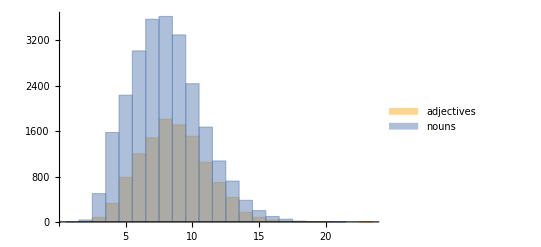

```mathematica
Histogram[{adjectivesData,nounData},]
```

I can also stack the data:

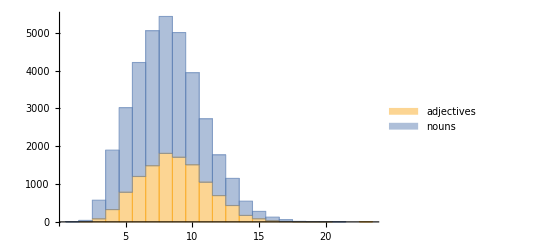

```mathematica
Histogram[{adjectivesData,nounData},ChartLayout->"Stacked",]
```

I can also make a row of histograms:

```mathematica
Histogram[{adjectivesData,nounData},ChartLayout->"Row"]
```

-Graphics-

Or a column of histograms:

```mathematica
Histogram[{adjectivesData,nounData},ChartLayout->"Column"]
```

-Graphics-

I will now apply different binning methods.

#### Sturges binning

```mathematica
Histogram[{adjectivesData,nounData},"Sturges",]
```

-Graphics-

The Sturges binning method computes the number of bins based on the length of data.

#### Scott binning

```mathematica
Histogram[{adjectivesData,nounData},"Scott",]
```

-Graphics-

The Scott binning method computes the number of bins by asymptotically minimizing the mean square.

#### Freedman-Diaconis binning

```mathematica
Histogram[{adjectivesData,nounData},"FreedmanDiaconis",]
```

-Graphics-

The Freedman-Diaconis binning method computes the number of bins by multiplying the interquartile range by two and then dividing by the cube root of the sample size.

#### Knuth

```mathematica
Histogram[{adjectivesData,nounData},"Knuth",]
```

-Graphics-

The Knuth binning method balances likelihood and prior probability of a piecewise uniform model.

#### Wand binning

```mathematica
Histogram[{adjectivesData,nounData},"Wand",]
```

-Graphics-

The Wand option uses one-level recursive approximate Wand binning to calculate the number of bins.

#### Count

I can visualize the counts of data points in each bin.

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"Count",ChartLayout->"Row"]
```

-Graphics-

#### Cumulative counts

I can visualize cumulative counts.

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"CumulativeCount",ChartLayout->"Row"]
```

-Graphics-

#### Survival counts

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"SurvivalCount",ChartLayout->"Row"]
```

-Graphics-

#### Probability

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"Probability",ChartLayout->"Row"]
```

-Graphics-

#### Intensity

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"Intensity",ChartLayout->"Row"]
```

-Graphics-

#### PDF probability density function

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"PDF",ChartLayout->"Row"]
```

-Graphics-

#### CDF cumulative distribution function

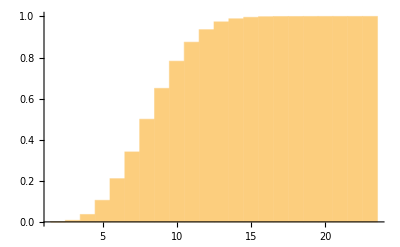

```mathematica
Histogram[adjectivesData,Automatic,"CDF",]
```

#### Survival function

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"SF",ChartLayout->"Row"]
```

-Graphics-

#### Hazard function

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"HF",ChartLayout->"Row"]
```

-Graphics-

#### Cumulative hazard function

```mathematica
Histogram[{adjectivesData,nounData},Automatic,"CHF",ChartLayout->"Row"]
```

-Graphics-

```mathematica
SmoothHistogram[{adjectivesData,nounData},PlotLayout->"Row"]
```

-Graphics-

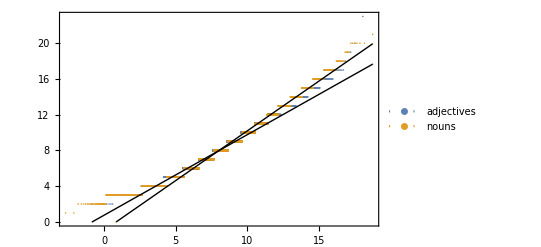

```mathematica
QuantilePlot[{adjectivesData,nounData},PlotLegends->{"adjectives","nouns"}]
```

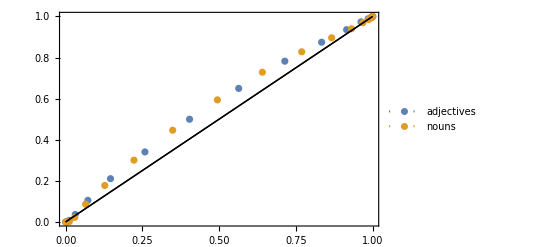

```mathematica
ProbabilityPlot[{adjectivesData,nounData},PlotLegends->{"adjectives","nouns"}]
```

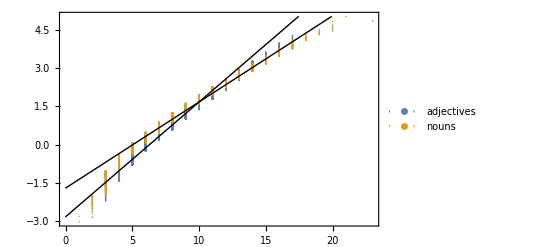

```mathematica
ProbabilityScalePlot[{adjectivesData,nounData},PlotLegends->{"adjectives","nouns"}]
```

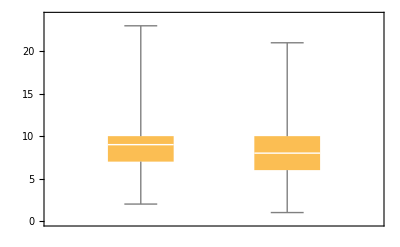

```mathematica
BoxWhiskerChart[{adjectivesData,nounData}]
```

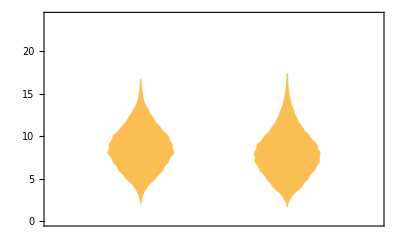

```mathematica
DistributionChart[{adjectivesData,nounData}]
```